```mathematica
data={{-4,13},{-2,25},{0,34},{2,42},{4,56}}
```

{{-4,13},{-2,25},{0,34},{2,42},{4,56}}

```mathematica
LinearModelFit[data,{1,x},x]
```

FittedModel[34.+5.15 x]

```mathematica
%124["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 34. | 0.778888 | 43.652 | 0.000026463
x | 5.15 | 0.275379 | 18.7015 | 0.000333724

```mathematica
data2={{-0.4,0.03},{-0.2,-0.16},{0,0.06},{0.2,0.09},{0.4,-0.08}}
```

{{-0.4,0.03},{-0.2,-0.16},{0,0.06},{0.2,0.09},{0.4,-0.08}}

```mathematica
mod=NonlinearModelFit[data2,a*Cos[10*x]+b*Sin[10*x],{a,b},x]
```

FittedModel[0.0553478 Cos[10 x]+0.110953 Sin[10 x]]

```mathematica
xs=data2[[All,1]];
lhs1=Total@Map[a*N@Cos[10*#]^2+b*N@Sin[10*#]*Cos[10*#]&,xs];
rhs1=Total@Map[#[[2]]*N@Cos[10*#[[1]]]&,data2];
lhs2=Total@Map[b*N@Sin[10*#]^2+a*N@Sin[10*#]*Cos[10*#]&,xs];
rhs2=Total@Map[#[[2]]*N@Sin[10*#[[1]]]&,data2];
Solve[{rhs1==lhs1,rhs2==lhs2},{a,b}]
```

{{a→0.0553478,b→0.110953}}

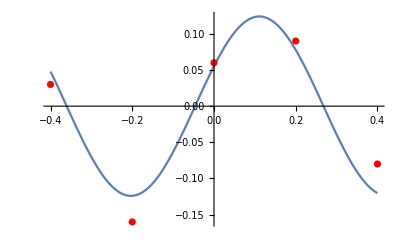

```mathematica
Show[Plot[mod[x],{x,-0.4,0.4},PlotRange->All],ListPlot[Style[data2,Red]]]
```